```mathematica
Quit[]
```

```mathematica
<<pkg`
```

```mathematica
m1=1.5;m2=1; λi=0;λf=2; ϵ=3/1000;
Rinit={1,.5,1.5};
Pinit=.1{1,-4,1};
S1init={1,1,1.3};
S2init={-7.5,-1.5,4.2};
(*end of user supplied  data*)
```

```mathematica
SeffLflow[m1,m2,Rinit,Pinit,S1init,S2init,λf,λi,ϵ]
NmSeffLflow[m1,m2,Rinit,Pinit,S1init,S2init,λf,λi,ϵ]
```

{{0.583617,-1.67448,0.596234},{-0.229294,-0.21203,-0.287171},{-0.245637,-1.85977,-0.413413},{-6.21165,1.37889,5.97111}}

{{0.583617,-1.67449,0.596234},{-0.229294,-0.21203,-0.287172},{-0.245638,-1.85977,-0.413415},{-6.21165,1.37889,5.97111}}

```mathematica
Jsqflow[m1,m2,Rinit,Pinit,S1init,S2init,λf,λi,ϵ]
NmJsqflow[m1,m2,Rinit,Pinit,S1init,S2init,λf,λi,ϵ]
Lsqflow[m1,m2,Rinit,Pinit,S1init,S2init,λf,λi,ϵ]
 NmLsqflow[m1,m2,Rinit,Pinit,S1init,S2init,λf,λi,ϵ]
Jzflow[m1,m2,Rinit,Pinit,S1init,S2init,λf,λi,ϵ]
NmJzflow[m1,m2,Rinit,Pinit,S1init,S2init,λf,λi,ϵ]
```

{{1.06557,-0.32913,1.50208},{-0.0221157,-0.421461,-0.0433732},{1.21465,0.187695,1.47627},{-7.712,-0.650693,4.0301}}

{{1.06557,-0.329133,1.50208},{-0.0221161,-0.421461,-0.0433736},{1.21465,0.187693,1.47628},{-7.712,-0.65069,4.0301}}

{{-1.00986,-0.451247,-1.50883},{-0.0939988,0.403603,-0.0909312},{1.,1.,1.3},{-7.5,-1.5,4.2}}

{{-1.00986,-0.451249,-1.50883},{-0.0939989,0.403603,-0.0909314},{1.,1.,1.3},{-7.5,-1.5,4.2}}

{{-0.870796,0.701224,1.5},{0.322104,0.257388,0.1},{-1.32544,0.493151,1.3},{4.48505,-6.19551,4.2}}

{{-0.870796,0.701224,1.5},{0.322104,0.257388,0.1},{-1.32544,0.493151,1.3},{4.48505,-6.19551,4.2}}

```mathematica
Hflow[5/2,1,2{ 1,1,1},1{1/2,-1/2,1/3},{0,1,1}N[√(3/1000) ],{1,-3/10,0}N[√(3/1000)],2,0,3/1000 ]
NmHflow[5/2,1,2{ 1,1,1},1{1/2,-1/2,1/3},{0,1,1}N[√(3/1000)] ,{1,-3/10,0}N[√(3/1000)],2,0 ,3/1000]
```

{{3.04302,0.39165,2.60131},{0.254268,-0.624495,0.107772},{0.0000407181,0.0547462,0.0547983},{0.0546817,-0.0165516,-0.000091835}}

{{{3.04337,0.39209,2.60149}},{{0.254342,-0.624397,0.107852}},{{0.0000384888,0.0547447,0.0547997}},{{0.0547503,-0.0165046,-0.0000304444}}}

The energy for the initial data is

-0.658364

The frequencies are

{-0.00990945,0.,1.61959,1.28479,-0.00151256}

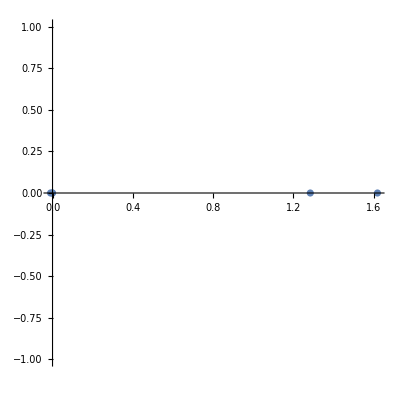

```mathematica
frequency[m1,m2,Rinit,Pinit,S1init,S2init,λf,λi,ϵ]
```

```mathematica
(*
(*data needed to check if the energy is negative*)
ϵ= 3/1000; 
 μ =m1  m2 /(m1+m2); M=m1+m2;
Q1=(1+3 m2/(4 m1));Q2=(1+3 m1/(4 m2));
Linit=Cross[Rinit, Pinit];
SeffLN=(Q1 S1init+ Q2 S2init).Linit;
En=μ ((Pinit.Pinit)/(2 μ^2)-(G M)/Norm[Rinit]) + (2 G ϵ SeffLN)/(Norm[Rinit])^3 //Simplify*)
```